```mathematica
f[x_]:=x/(Exp[x]-1)-1+x/2
Simplify[f[x]-f[-x]]
```

0

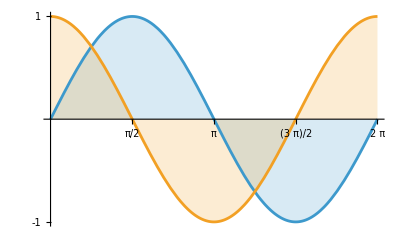

```mathematica
Plot[{Sin[x],Cos[x]},{x, 0, 2Pi},Ticks->{{Pi/2,Pi,3Pi/2,2Pi},{-1,1}},Filling->Axis]
```

```mathematica
Plot3D[x+Sin[x^2+y^2],{x,-4, 4},{y,-4,4},PlotPoints->50,ColorFunction->"FruitPunchColors"]
```

-Graphics3D-

```mathematica
ContourPlot[x+Sin[x^2+y^2],{x,-4, 4},{y,-4,4},PlotPoints->50,ColorFunction->"GreenPinkTones"]
```

-Graphics-

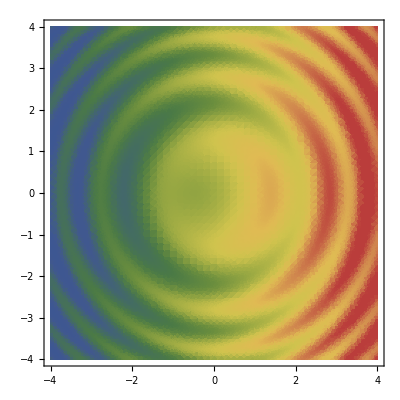

```mathematica
DensityPlot[x+Sin[x^2+y^2],{x,-4, 4},{y,-4,4},PlotPoints->50,ColorFunction->"DarkRainbow"]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
ContourPlot3D[20x(3y^2-x^2)-24(x^2+y^2)+3z^2==0,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,PlotPoints->70]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+v*Cos[u/2])Cos[u],(2+v*Cos[u/2])Sin[u],v*Sin[u/2]},{u,0,2Pi},{v,-1/2,1/2},Mesh->{3,4}]
```

-Graphics3D-

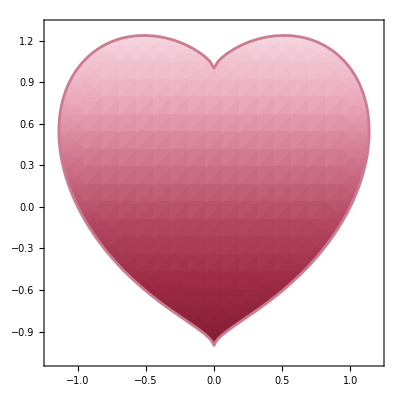

```mathematica
RegionPlot[(x^2+y^2-1)^3-x^2y^3<0,{x,-1.2,1.2},{y,-1.1,1.3},ColorFunction->"ValentineTones"]
```

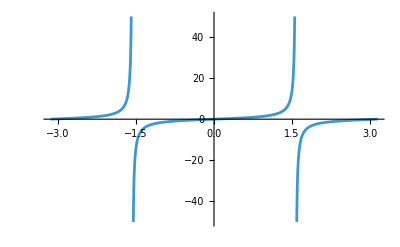

```mathematica
Plot[Tan[x],{x,-Pi,Pi},PlotRange->{-50,50}]
```

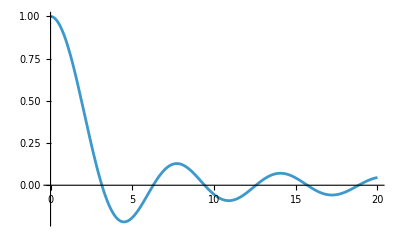

```mathematica
Plot[Sin[x]/x,{x,0,20},PlotRange->All]
```

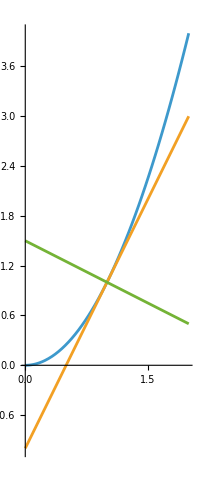

```mathematica
f[x_]:=x^2
t[x_]:=2(x-1)+1
n[x_]:=-1/2(x-1)+1
Plot[{f[x],t[x],n[x]},{x,0,2},AspectRatio->Automatic]
```

```mathematica
"Přímky nebudou kolmé, když osy nebudou mít stejné měřítko"
```

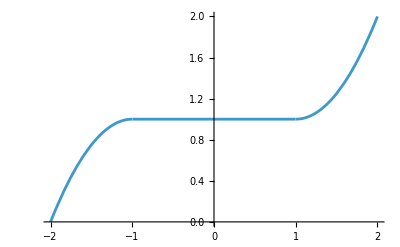

```mathematica
Plot[Piecewise[{{-(x+1)^2+1,x<-1},{1,-1<=x<=1},{(x-1)^2+1,x>1}}],{x,-2,2},PlotRange->Full]
```

```mathematica
f[a_]:=x^2/a^2+y^2/(1-a)^2==1
```

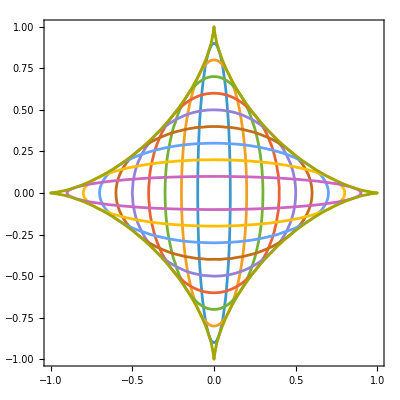

```mathematica
ContourPlot[{Evaluate[Table[f[a/10],{a,1,9}]],Abs[x]^(2/3)+Abs[y]^(2/3)==1},{x,-1,1},{y,-1,1}]
```

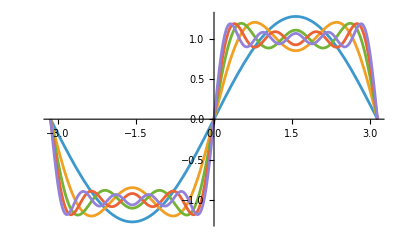

```mathematica
Plot[Evaluate[Table[4/Pi*Sum[Sin[(2n-1)x]/(2n-1),{n,1,l}],{l,1,5}]],{x,-Pi,Pi}]
```

```mathematica
ContourPlot[Re[((x+I*y)^2+(1)/(16(x+I*y)^2))^3], {x, -1.5, 1.5}, {y, -1.5, 1.5}, PlotPoints->100, Contours->{0,1/2,-1/2,1,-1,2,-2,5,-5}]
```

-Graphics-

```mathematica
c=-0.6
ContourPlot3D[(1-(x^2+y^2+z^2))^3-5/27*c*(x^2+y^2+z^2)+c*(z(-2x(x^4-10x^2*y^2+5y^4)-5(x^2+y^2)^2*z+5(x^2+y^2)^2*z^3-z^5))==0,{x, -5, 5}, {y, -5, 5}, {z, -5, 5}, Mesh->None, PlotPoints->40, ContourStyle->{Specularity[White, 100], Orange}]
```

-0.6

-Graphics3D-

```mathematica
c=-0.3
ContourPlot3D[(1-(x^2+y^2+z^2))^3-5/27*c*(x^2+y^2+z^2)+c*(z(-2x(x^4-10x^2*y^2+5y^4)-5(x^2+y^2)^2*z+5(x^2+y^2)^2*z^3-z^5))==0,{x, -5, 5}, {y, -5, 5}, {z, -5, 5}, Mesh->None, PlotPoints->40, ContourStyle->{Specularity[White, 100], Orange}]
```

-0.3

-Graphics3D-

```mathematica
c=3
ContourPlot3D[(1-(x^2+y^2+z^2))^3-5/27*c*(x^2+y^2+z^2)+c*(z(-2x(x^4-10x^2*y^2+5y^4)-5(x^2+y^2)^2*z+5(x^2+y^2)^2*z^3-z^5))==0,{x, -5, 5}, {y, -5, 5}, {z, -5, 5}, Mesh->None, PlotPoints->40, ContourStyle->{Specularity[White, 100], Orange}]
```

3

-Graphics3D-

```mathematica
c=81
ContourPlot3D[(1-(x^2+y^2+z^2))^3-5/27*c*(x^2+y^2+z^2)+c*(z(-2x(x^4-10x^2*y^2+5y^4)-5(x^2+y^2)^2*z+5(x^2+y^2)^2*z^3-z^5))==0,{x, -5, 5}, {y, -5, 5}, {z, -5, 5}, Mesh->None, PlotPoints->40, ContourStyle->{Specularity[White, 100], Orange}]
```

81

-Graphics3D-